# (*Didinium -- Flow Field*)

```mathematica
(*Parameters*)
n=12;
ρvar=1.3;
θvar=30π/180;
ϕvar=14π/180;
radius=ρvar Sin[θvar];
n1=24;
n2=48;
ρ2var=1.3;
θ2var=100π/180;
radius2=ρ2var Sin[θ2var];
arrowLength=0.2;
shaftRadius=0.01;
headLength=0.1;
headRadius=0.05;

Gbulk[Xx_:{x,y,z},Xy_:{xs,ys,zs}]:=Module[{RX=Xx-Xy,δ=IdentityMatrix[3]},
Table[δ⟦j,k⟧/(√(RX.RX))+(RX⟦j⟧RX⟦k⟧)/(RX.RX)^(3/2),{j,1,3},{k,1,3}]]
GbulkLap[{x_,y_,z_},{xs_,ys_,zs_}]:=Evaluate[FullSimplify[Laplacian[Gbulk[{x,y,z},{xs,ys,zs}]⟦All,3⟧,{xs,ys,zs}]]]
Gsphere[Xx_:{x,y,z},Xy_:{xf,yf,zf},XyB_:{xs,ys,zs},A_:1]:=Module[{Xys=A^2/(Xy.Xy)Xy,RX=Xx-Xy-XyB,RXs=Xx-A^2/(Xy.Xy)Xy-XyB,rX=√((Xx-Xy-XyB).(Xx-Xy)-XyB),rXs=√((Xx-A^2/(Xy.Xy)Xy-XyB).(Xx-A^2/(Xy.Xy)Xy-XyB)),XyF=Xy,XxB=Xx-XyB,δ=IdentityMatrix[3]},Table[
-A/(√(XyF.XyF))δ⟦j,k⟧/rXs-A^3/(XyF.XyF)^(3/2)(RXs⟦j⟧RXs⟦k⟧)/rXs^3-(XyF.XyF-A^2)/(√(XyF.XyF))((Xys⟦j⟧ Xys⟦k⟧)/(A^3 rXs)-A/((XyF.XyF) rXs^3)(Xys⟦j⟧RXs⟦k⟧+Xys⟦k⟧RXs⟦j⟧)+(2Xys⟦j⟧Xys⟦k⟧(Xys.RXs))/(A^3 rXs^3))-((XxB.XxB)-A^2)(((XyF.XyF)-A^2)/(2 (XyF.XyF)^(3/2)))(
(-3RXs⟦j⟧XyF⟦k⟧)/(A rXs^3)+A δ⟦j,k⟧/rXs^3-3A (RXs⟦j⟧RXs⟦k⟧)/rXs^5-(2Xys⟦j⟧XyF⟦k⟧)/(A rXs^3)+(6RXs⟦j⟧XyF⟦k⟧)/(A rXs^5)Xys.RXs+(3A)/(Xys.Xys)(RXs⟦j⟧Xys⟦k⟧rXs^2+RXs⟦j⟧RXs⟦k⟧ (Xys.Xys)+(rXs-√(Xys.Xys))rXs^2 √(Xys.Xys)δ⟦j,k⟧)/(rXs^3(rXs √(Xys.Xys)+XxB.Xys-Xys.Xys))-(3A)/(Xys.Xys)(((√(Xys.Xys)RXs⟦j⟧+rXs Xys⟦j⟧)(Xys⟦k⟧rXs^2-Xys.Xys RXs⟦k⟧+(XxB⟦k⟧-2Xys⟦k⟧)rXs √(Xys.Xys)))/(rXs^2(rXs √(Xys.Xys)+XxB.Xys-Xys.Xys)^2))-(3A)/(Xys.Xys)(XxB⟦j⟧Xys⟦k⟧+√(XxB.XxB)√(Xys.Xys)δ⟦j,k⟧)/(√(XxB.XxB)(√(XxB.XxB)√(Xys.Xys)+XxB.Xys))+(3A)/(Xys.Xys)((√(Xys.Xys)XxB⟦j⟧+√(XxB.XxB)Xys⟦j⟧)(√(Xys.Xys)XxB⟦k⟧+√(XxB.XxB)Xys⟦k⟧))/(√(XxB.XxB)(√(XxB.XxB)√(Xys.Xys)+XxB.Xys)^2)) 
,{j,1,3},{k,1,3}]]
uSwimmerN[{x_,y_,z_},{xs_,ys_,zs_},{zf_,ρf_},A_,V_,Ω_,NN_Integer]:=Module[
{RXX={x,y,z}-{xs,ys,zs},Fz=-1/NN 1/(1-(A^3 (-2 zf^2+ρf^2)+3 A (zf^2+ρf^2) (2 zf^2+ρf^2))/(4(zf^2+ρf^2)^(5/2)))(6A V)/8,Fϕ=1/NN 1/(1-(A^2/(zf^2+ρf^2))^(3/2))(A^3 Ω)/ρf},
(3A V)/4(Gbulk[{x,y,z},{xs,ys,zs}]⟦All,3⟧+A^2/6 GbulkLap[{x,y,z},{xs,ys,zs}])
+A^3/Norm[RXX]^3 Cross[{0,0,Ω},RXX]
+Sum[(Gbulk[{x,y,z},{xs,ys,zs}+{ρf Cos[2π(i-1)/NN],ρf Sin[2π(i-1)/NN],zf}]+Gsphere[{x,y,z},{ρf Cos[2π(i-1)/NN],ρf Sin[2π(i-1)/NN],zf},{xs,ys,zs},A]).{Fϕ Sin[2π(i-1)/NN],-Fϕ Cos[2π(i-1)/NN],Fz},{i,1,NN}]
]
```

# (*Force arrow plots*)

## (*Straight*)

```mathematica
1-(A^3 (-2 zf^2+ρf^2)+3 A (zf^2+ρf^2) (2 zf^2+ρf^2))/(4(zf^2+ρf^2)^(5/2))/.{zf->ρvar Cos[θvar],ρf->ρvar Sin[θvar],zf2->ρ2var Cos[θ2var],ρf2->ρ2var Sin[θ2var],A->1,V->1,NN->12,MM->12,Θ->0.π/180}
1-(A^3 (-2 zf2^2+ρf2^2)+3 A (zf2^2+ρf2^2) (2 zf2^2+ρf2^2))/(4(zf2^2+ρf2^2)^(5/2))/.{zf->ρvar Cos[θvar],ρf->ρvar Sin[θvar],zf2->ρ2var Cos[θ2var],ρf2->ρ2var Sin[θ2var],A->1,V->1,NN->12,MM->12,Θ->0.π/180}
```

0.132624

0.302183

```mathematica
(*Function to create a single tube arrow*)
tubeArrow[base_,dir_]:=Module[{shaftEnd,headBase,headTip},shaftEnd=base+dir (1-headLength/arrowLength);
headBase=shaftEnd;
headTip=base+dir;
{Tube[{base,shaftEnd},shaftRadius],Cone[{headBase,headTip},headRadius]}]

(*Generate arrows*)
arrows=Table[Module[{theta,base,dir},theta=2 Pi k/n;
(*Base point on ring*)base={radius Cos[theta],radius Sin[theta],ρvar Cos[θvar]};
(*z direction*)dir=arrowLength {0,0,-1};
(*Tangential direction *)(*dir=arrowLength {-Sin[theta],Cos[theta],0};*)
tubeArrow[base,dir]],{k,0,n-1}];

axes=Table[Graphics3D[{White,tubeArrow[{1,-1/2,-1},0.3k]}],{k,{{1,0,0},{0,1,0},{0,0,1}}}];

(*Render*)
plotToSave=Show[
Graphics3D[{Opacity[0.25],Green,Sphere[{0,0,0},1]}],
Graphics3D[{Red,arrows}],
Graphics3D[{Blue,tubeArrow[{0,0,0},{0,0,0.65}]}],
Background->Black,ImageSize->800{1,1},Boxed->False,Axes->False,Lighting->"Neutral",ViewVector->{{2,2,1.5},{0,0,0.1}},ViewVertical->{0, 0, 1},ViewAngle->50π/180]
SetDirectory[NotebookDirectory[]];
Export["ArrowsA.jpg",plotToSave]
```

-Graphics3D-

ArrowsA.jpg

## (*Spinner*)

```mathematica
(1-(A^2/(zf^2+ρf^2))^(3/2))/.{zf->ρvar Cos[θvar],ρf->ρvar Sin[θvar],zf2->ρ2var Cos[θ2var],ρf2->ρ2var Sin[θ2var],A->1,V->1,NN->12,MM->12,Θ->0.π/180}
(1-(A^2/(zf2^2+ρf2^2))^(3/2))/.{zf->ρvar Cos[θvar],ρf->ρvar Sin[θvar],zf2->ρ2var Cos[100 π/180.],ρf2->ρ2var Sin[100 π/180.],A->1,V->1,NN->12,MM->12,Θ->0.π/180}
```

0.544834

0.544834

```mathematica
θvar 180./π
```

30.

```mathematica
(*Function to create a single tube arrow*)
tubeArrow[base_,dir_]:=Module[{shaftEnd,headBase,headTip},shaftEnd=base+dir (1-headLength/arrowLength);
headBase=shaftEnd;
headTip=base+dir;
{Tube[{base,shaftEnd},shaftRadius],Cone[{headBase,headTip},headRadius]}]

(*Generate arrows*)
arrows=Table[Module[{theta,base,dir},theta=2 Pi k/n;
(*Base point on ring*)base={radius Cos[theta],radius Sin[theta],ρvar Cos[θvar]};
(*Tangential direction *)dir=arrowLength {Sin[theta],-Cos[theta],0};
tubeArrow[base,dir]],{k,0,n-1}];
arrowsB=Table[Module[{theta,base,dir},theta=2 Pi k/4+π/4;
(*Base point on ring*)base=0.5{ Cos[theta],Sin[theta],0};
(*Tangential direction *)dir=0.15 {-Sin[theta],Cos[theta],0};
tubeArrow[base,dir]],{k,0,4-1}];
ring=ParametricPlot3D[{(0.5+0.01 Cos[v]) Cos[u],(0.5+0.01Cos[v]) Sin[u],0.01 Sin[v]},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->Blue,Mesh->None];

(*Render*)
plotToSave=Show[
Graphics3D[{Opacity[0.25],Green,Sphere[{0,0,0},1]}],
Graphics3D[{Red,arrows}],Graphics3D[{Blue,arrowsB}],ring,
Background->Black,ImageSize->800{1,1},Boxed->False,Axes->False,Lighting->"Neutral",ViewVector->{{2,2,1.5},{0,0,0.1}},ViewVertical->{0, 0, 1},ViewAngle->50π/180]
SetDirectory[NotebookDirectory[]];
Export["ArrowsB.jpg",plotToSave]
```

-Graphics3D-

ArrowsB.jpg

## (*Didinium*)

```mathematica
(*Function to create a single tube arrow*)
tubeArrow[base_,dir_]:=Module[{shaftEnd,headBase,headTip},shaftEnd=base+dir (1-headLength/arrowLength);
headBase=shaftEnd;
headTip=base+dir;
{Tube[{base,shaftEnd},shaftRadius],Cone[{headBase,headTip},headRadius]}]

(*Generate arrows*)
arrows=Table[Module[{theta,base,dir},theta=2 Pi k/n1;
(*Base point on ring*)base={radius Cos[theta],radius Sin[theta],ρvar Cos[θvar]};
(*direction *)dir=arrowLength {Sin[theta]Sin[ϕvar],-Cos[theta]Sin[ϕvar],-Cos[ϕvar]};
tubeArrow[base,dir]],{k,0,n1-1}];
arrows2=Table[Module[{theta,base,dir},theta=2 Pi k/n2;
(*Base point on ring*)base={radius2 Cos[theta],radius2 Sin[theta],ρvar Cos[θ2var]};
(*direction *)dir=arrowLength {Sin[theta]Sin[ϕvar],-Cos[theta]Sin[ϕvar],-Cos[ϕvar]};
tubeArrow[base-dir,dir]],{k,0,n2-1}];

(*Render*)
plotToSave=Show[
Graphics3D[{Opacity[0.25],Green,Sphere[{0,0,0},1]}],
Graphics3D[{Red,arrows}],Graphics3D[{Red,arrows2}],
Graphics3D[{Blue,tubeArrow[{0,0,0},{0,0,0.65}]}],Graphics3D[{Blue,arrowsB}],ring,
Background->Black,ImageSize->800{1,1},Boxed->False,Axes->False,Lighting->"Neutral",ViewVector->{{2,2,1.5},{0,0,0.1}},ViewVertical->{0, 0, 1},ViewAngle->50π/180]
SetDirectory[NotebookDirectory[]]
Export["ArrowsC.jpg",plotToSave]
```

-Graphics3D-

/Users/amaths/Library/CloudStorage/Box-Box/Mathijssen/My Publications/2026-01 Guillermina Didinium/S4

ArrowsC.jpg

```mathematica
plotToSave=Show[
Graphics3D[{Opacity[0.25],Green,Sphere[{0,0,0},1]}],
Graphics3D[{Red,arrows}],Graphics3D[{Red,arrows2}],
Graphics3D[{Blue,tubeArrow[{0,0,0},{0,0,0.65}]}],Graphics3D[{Blue,arrowsB}],ring,
Background->White,ImageSize->800{1,1},Boxed->False,Axes->False,Lighting->"Neutral",ViewVector->{{2,2,1.5},{0,0,0.1}},ViewVertical->{0, 0, 1},ViewAngle->50π/180,AspectRatio->1.1]
SetDirectory[NotebookDirectory[]]
Export["DidiniumModel.jpg",plotToSave]
```

-Graphics3D-

/Users/amaths/Library/CloudStorage/Box-Box/Mathijssen/My Publications/2026-01 Guillermina Didinium/S4

DidiniumModel.jpg

# (*Flows - Straight swimmer*)

## (*Plot flow in lab frame*)

-Graphics-

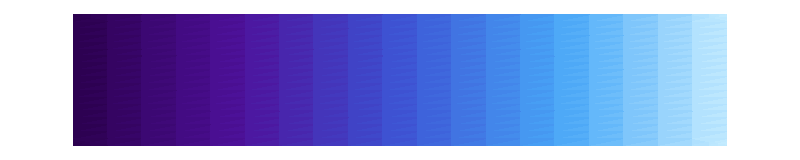

```mathematica
mm=3;mmoff=-0.5;rl=0;rr=1;
uPlot=uSwimmerN[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},1,1,0,12];
uPlot={uPlot⟦3⟧,uPlot⟦1⟧};
FlowALabPlot=Show[DensityPlot[Evaluate[N[Norm[uPlot]]],{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},PlotRange->{-10000rl,10000rr},
ColorFunctionScaling->False,ColorFunction->(ColorData["DeepSeaColors"][((If[#>rr,rr,If[#<-rl,-rl,#]]+rl)/(rl+rr))]&),PlotPoints->200],
VectorPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},VectorColorFunction->None,VectorStyle->Black,VectorPoints->8,VectorScaling->None,VectorSizes->1],
(*StreamPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},StreamColorFunction->None,StreamStyle->Black,StreamPoints->{Automatic,0.8},StreamScale->Large],*)
StreamPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},StreamColorFunction->None,StreamPoints->{Automatic,0.2},StreamScale->None],
Graphics[{Thick,Black,Disk[{0,0},1]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],Sin[θvar]},0.05]}],
Frame->False,LabelStyle->{FontSize->20,FontFamily->"Arial"},PlotRangePadding->None,ImageSize->800]
LegendToSave=Show[DensityPlot[x/5,{x,0,5},{y,0,1},AspectRatio->Automatic,
ColorFunctionScaling->False,ColorFunction->(ColorData["DeepSeaColors"][#]&),PlotPoints->20],
Frame->False,PlotRangePadding->None]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FlowALab.jpg",FlowALabPlot];
Export["FlowALegend.jpg",LegendToSave];
NotebookSave[];
```

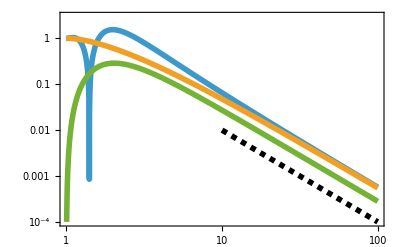

```mathematica
uPlot=uSwimmerN[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},1,1,0,12];
ScalePlotA=Show[
LogLogPlot[Evaluate[
{Norm[uPlot⟦3⟧]/.{x->0,z->r},
Norm[uPlot⟦3⟧]/.{x->0,z->-r},
Norm[uPlot⟦1⟧]/.{z->0,x->r}}]
,{r,1,100},Frame->True,PlotRange->{10^-4,3},PlotStyle->Thickness[0.01],AspectRatio->GoldenRatio^-1],
LogLogPlot[1/z^2,{z,10,100},PlotStyle->{Thickness[0.01], Dashing[0.01],Black}],
LabelStyle->{FontSize->40,FontFamily->"Arial"},ImageSize->800{1,GoldenRatio^-1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["ScalePlotA.jpg",ScalePlotA];
NotebookSave[];
```

# (*Spinner*)

-Graphics-

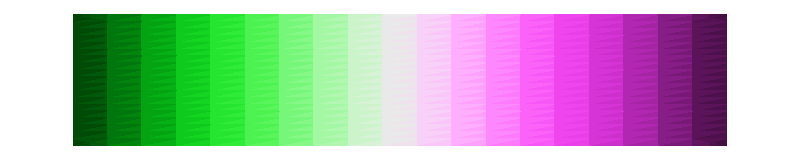

```mathematica
mm=3;mmoff=-0.5;rl=-1.;rr=1.;
uPlot=uSwimmerN[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},1,0,1,12];
uPlot=-uPlot⟦2⟧;
FlowBLabPlot=Show[DensityPlot[Evaluate[N[uPlot]],{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},PlotRange->{-10000,10000},
ColorFunctionScaling->False,ColorFunction->(ColorData["GreenPinkTones"][((If[#>rr,rr,If[#<rl,rl,#]]-rl)/(rr-rl))]&),PlotPoints->200],
Graphics[{Thick,Black,Disk[{0,0},1]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],-Sin[θvar]},0.05]}],
Frame->False,LabelStyle->{FontSize->20,FontFamily->"Arial"},PlotRangePadding->None,ImageSize->800]
LegendToSave=Show[DensityPlot[x/5,{x,0,5},{y,0,1},AspectRatio->Automatic,
ColorFunctionScaling->False,ColorFunction->(ColorData["GreenPinkTones"][#]&),PlotPoints->20],
Frame->False,PlotRangePadding->None]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FlowBLab.jpg",FlowBLabPlot];
Export["FlowBLegend.jpg",LegendToSave];
NotebookSave[];
```

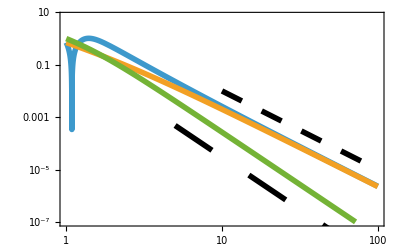

```mathematica
uPlot=uSwimmerN[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},1,0,1,12];
ScalePlotB=Show[
LogLogPlot[Evaluate[
{Norm[uPlot⟦2⟧]/.{x->r Sin[π/4],z->r Cos[π/4]},
Norm[uPlot⟦2⟧]/.{x->r Sin[3π/4],z->r Cos[3π/4]},
Norm[uPlot⟦2⟧]/.{z->0,x->r}}]
,{r,1,100},Frame->True,PlotRange->{10^-7,7},PlotStyle->Thickness[0.01],AspectRatio->GoldenRatio^-1],
LogLogPlot[10/z^3,{z,10,100},PlotStyle->{Thickness[0.01], Dashing[0.04], Black}],
LogLogPlot[0.3/z^4,{z,5,100},PlotStyle->{Thickness[0.01], Dashing[0.08],Black}],
LabelStyle->{FontSize->40,FontFamily->"Arial"},ImageSize->800{1,GoldenRatio^-1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["ScalePlotB.jpg",ScalePlotB];
NotebookSave[];
```

# (*Didinium*)

```mathematica
uSwimmerNM[{x_,y_,z_},{xs_,ys_,zs_},{zf_,ρf_},{zf2_,ρf2_},A_,V_,Ω_,NN_Integer,MM_Integer]:=Module[
{RXX={x,y,z}-{xs,ys,zs},
Fz=-1/((1-(A^3 (-2 zf^2+ρf^2)+3 A (zf^2+ρf^2) (2 zf^2+ρf^2))/(4(zf^2+ρf^2)^(5/2)))NN+(1-(A^3 (-2 zf2^2+ρf2^2)+3 A (zf2^2+ρf2^2) (2 zf2^2+ρf2^2))/(4(zf2^2+ρf2^2)^(5/2)))MM)(6A V)/8,
Fϕ=1/(ρf(1-(A^2/(zf^2+ρf^2))^(3/2))NN+ρf2(1-(A^2/(zf2^2+ρf2^2))^(3/2))MM)A^3 Ω},
(*Print[Fz];
Print[Fϕ];
Print[ArcTan[Fϕ/Fz]180./π];*)
(3A V)/4(Gbulk[{x,y,z},{xs,ys,zs}]⟦All,3⟧+A^2/6 GbulkLap[{x,y,z},{xs,ys,zs}])
+A^3/Norm[RXX]^3 Cross[{0,0,Ω},RXX]
+Sum[(Gbulk[{x,y,z},{xs,ys,zs}+{ρf Cos[2π(i-1)/NN],ρf Sin[2π(i-1)/NN],zf}]+Gsphere[{x,y,z},{ρf Cos[2π(i-1)/NN],ρf Sin[2π(i-1)/NN],zf},{xs,ys,zs},A]).{Fϕ Sin[2π(i-1)/NN],-Fϕ Cos[2π(i-1)/NN],Fz},{i,1,NN}]
+Sum[(Gbulk[{x,y,z},{xs,ys,zs}+{ρf2 Cos[2π(i-1)/MM],ρf2 Sin[2π(i-1)/MM],zf2}]+Gsphere[{x,y,z},{ρf2 Cos[2π(i-1)/MM],ρf2 Sin[2π(i-1)/MM],zf2},{xs,ys,zs},A]).{Fϕ Sin[2π(i-1)/MM],-Fϕ Cos[2π(i-1)/MM],Fz},{i,1,MM}]
]
```

## (*Lab frame*)

{1.3,1.3,30.,100.}

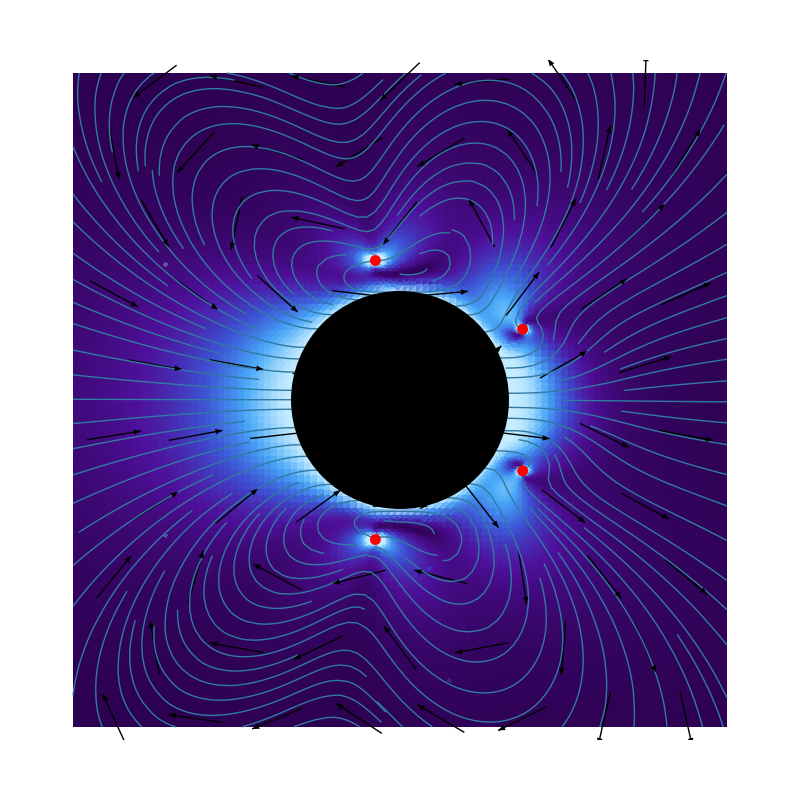

-Graphics-

```mathematica
mm=3;mmoff=0;rl=0;rr=1;
{ρvar,ρ2var,θvar 180./π,θ2var 180./π}
uPlot=uSwimmerNM[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},ρ2var{Cos[θ2var],Sin[θ2var]},1.,1.,0 0.4438,24,48];
uPlot={uPlot⟦3⟧,uPlot⟦1⟧};
FlowCLabPlot=Show[DensityPlot[Evaluate[N[Norm[uPlot]]],{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},PlotRange->{-1000,1000},
ColorFunctionScaling->False,ColorFunction->(ColorData["DeepSeaColors"][((If[#>rr,rr,If[#<rl,rl,#]]-rl)/(rr-rl))]&),PlotPoints->100],
VectorPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},VectorColorFunction->None,VectorStyle->Black,VectorPoints->8,VectorScaling->None,VectorSizes->1],
(*StreamPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},StreamColorFunction->None,StreamStyle->Black,StreamPoints->{Automatic,0.8},StreamScale->Large],*)
StreamPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},StreamColorFunction->None,StreamPoints->{Automatic,0.2},StreamScale->None],
Graphics[{Thick,Black,Disk[{0,0},1]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],-Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρ2var{Cos[θ2var],Sin[θ2var]},0.05]}],
Graphics[{Thick,Red,Disk[ρ2var{Cos[θ2var],-Sin[θ2var]},0.05]}],
Frame->False,LabelStyle->{FontSize->20,FontFamily->"Arial"},PlotRangePadding->None,ImageSize->800]
LegendToSave=Show[DensityPlot[x/5,{x,0,5},{y,0,1},AspectRatio->Automatic,
ColorFunctionScaling->False,ColorFunction->(ColorData["DeepSeaColors"][#]&),PlotPoints->20],
Frame->False,PlotRangePadding->None]
```

{1.3,1.3,30.,100.}

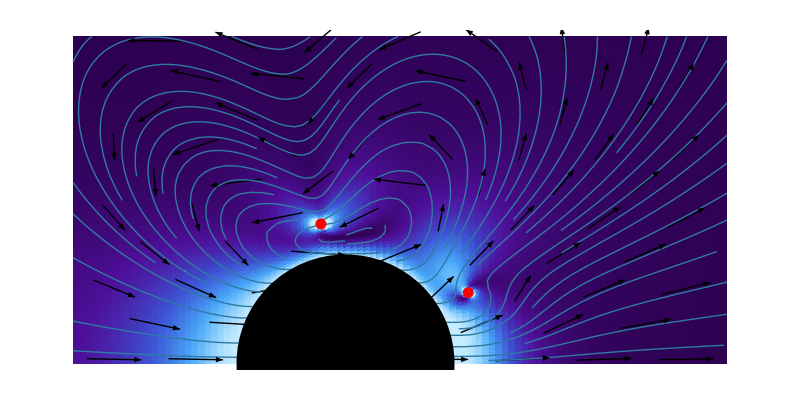

```mathematica
mm=3;mmoff=-0.5;rl=0;rr=1;
{ρvar,ρ2var,θvar 180./π,θ2var 180./π}
uPlot=uSwimmerNM[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},ρ2var{Cos[θ2var],Sin[θ2var]},1.,1.,0 0.4438,24,48];
uPlot={uPlot⟦3⟧,uPlot⟦1⟧};
FlowCLabPlot=Show[DensityPlot[Evaluate[N[Norm[uPlot]]],{z,-mm-mmoff,mm-mmoff},{x,0,mm},PlotRange->{-1000,1000},
ColorFunctionScaling->False,ColorFunction->(ColorData["DeepSeaColors"][((If[#>rr,rr,If[#<rl,rl,#]]-rl)/(rr-rl))]&),PlotPoints->100,AspectRatio->Automatic],
VectorPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,0,mm},VectorColorFunction->None,VectorStyle->Black,VectorPoints->8,VectorScaling->None,VectorSizes->1],
(*StreamPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},StreamColorFunction->None,StreamStyle->Black,StreamPoints->{Automatic,0.8},StreamScale->Large],*)
StreamPlot[uPlot,{z,-mm-mmoff,mm-mmoff},{x,0,mm},StreamColorFunction->None,StreamPoints->{Automatic,0.2},StreamScale->None],
Graphics[{Thick,Black,Disk[{0,0},1]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρ2var{Cos[θ2var],Sin[θ2var]},0.05]}],
Frame->False,LabelStyle->{FontSize->20,FontFamily->"Arial"},PlotRangePadding->None,ImageSize->800{1,0.5}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FlowCLab.jpg",FlowCLabPlot];
NotebookSave[];
```

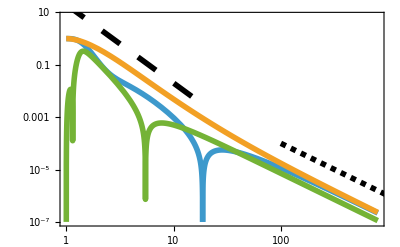

```mathematica
uPlot=uSwimmerNM[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},ρ2var{Cos[θ2var],Sin[θ2var]},1.,1.,0 0.4438,24,48];
ScalePlotC=Show[
(*LogLogPlot[Norm[uPlot⟦3⟧]/.{x->0},{z,1,800},Frame->True,PlotRange->{10^-7,1}],*)
LogLogPlot[Evaluate[
{Norm[uPlot⟦3⟧]/.{x->0,z->r},
Norm[uPlot⟦3⟧]/.{x->0,z->-r},
Norm[uPlot⟦1⟧]/.{z->0,x->r}}]
,{r,1,800},Frame->True,PlotRange->{10^-7,7},PlotStyle->Thickness[0.01],AspectRatio->GoldenRatio^-1],
LogLogPlot[1/z^2,{z,100,1000},PlotStyle->{Thickness[0.01], Dashing[0.01], Black}],
LogLogPlot[20/z^3,{z,1,20},PlotStyle->{Thickness[0.01], Dashing[0.04], Black}]
,LabelStyle->{FontSize->40,FontFamily->"Arial"},ImageSize->800{1,GoldenRatio^-1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["ScalePlotC.jpg",ScalePlotC];
NotebookSave[];
```

## (*Rest frame*)

{1.3,1.3,30.,100.}

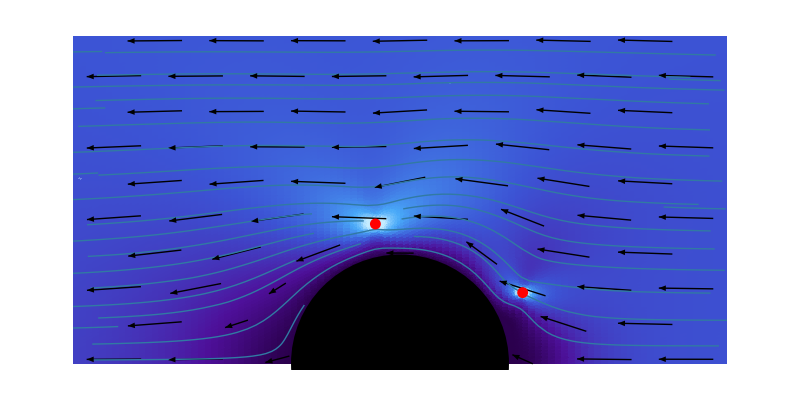

```mathematica
mm=3;mmoff=0;rl=0;rr=2;
{ρvar,ρ2var,θvar 180./π,θ2var 180./π}
uPlot=uSwimmerNM[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},ρ2var{Cos[θ2var],Sin[θ2var]},1.,1.,0.4438,24,48];
uPlot={uPlot⟦3⟧,uPlot⟦1⟧};
FlowCRestPlot=Show[DensityPlot[Evaluate[N[Norm[{-1,0}+uPlot]]],{z,-mm-mmoff,mm-mmoff},{x,0,mm},PlotRange->{-1000,1000},
ColorFunctionScaling->False,ColorFunction->(ColorData["DeepSeaColors"][((If[#>rr,rr,If[#<rl,rl,#]]-rl)/(rr-rl))]&),PlotPoints->100,AspectRatio->Automatic],
VectorPlot[{-1,0}+uPlot,{z,-mm-mmoff,mm-mmoff},{x,0,mm},VectorColorFunction->None,VectorStyle->Black,VectorPoints->8,VectorScaling->None,VectorSizes->1],
(*StreamPlot[{-1,0}+uPlot,{z,-mm-mmoff,mm-mmoff},{x,-mm,mm},StreamColorFunction->None,StreamStyle->Black,StreamPoints->{Automatic,0.8},StreamScale->Large],*)
StreamPlot[{-1,0}+uPlot,{z,-mm-mmoff,mm-mmoff},{x,0,mm},StreamColorFunction->None,StreamPoints->{Automatic,0.2},StreamScale->None],
Graphics[{Thick,Black,Disk[{0,0},1]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],-Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρ2var{Cos[θ2var],Sin[θ2var]},0.05]}],
Graphics[{Thick,Red,Disk[ρ2var{Cos[θ2var],-Sin[θ2var]},0.05]}],
Frame->False,LabelStyle->{FontSize->20,FontFamily->"Arial"},PlotRangePadding->None,ImageSize->800{1,0.5}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FlowCRest.jpg",FlowCRestPlot];
NotebookSave[];
```

## (*Spinning*)

{1.3,1.3,30.,100.}

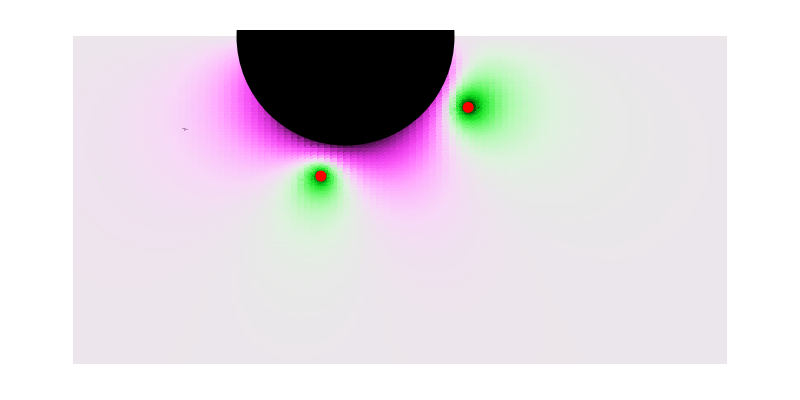

```mathematica
mm=3;mmoff=-0.5;rl=-1;rr=1;
{ρvar,ρ2var,θvar 180./π,θ2var 180./π}
uPlot=uSwimmerNM[{x,0,z},{0,0,0},ρvar{Cos[θvar],Sin[θvar]},ρ2var{Cos[θ2var],Sin[θ2var]},1.,1.,0.4438,24,48];
uPlot=-1/0.4438 uPlot⟦2⟧;
FlowCRotPlot=Show[DensityPlot[Evaluate[N[uPlot]],{z,-mm-mmoff,mm-mmoff},{x,-mm,0},PlotRange->{-10000,10000},
ColorFunctionScaling->False,ColorFunction->(ColorData["GreenPinkTones"][((If[#>rr,rr,If[#<rl,rl,#]]-rl)/(rr-rl))]&),PlotPoints->100,AspectRatio->Automatic],
Graphics[{Thick,Black,Disk[{0,0},1]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρvar{Cos[θvar],-Sin[θvar]},0.05]}],
Graphics[{Thick,Red,Disk[ρ2var{Cos[θ2var],Sin[θ2var]},0.05]}],
Graphics[{Thick,Red,Disk[ρ2var{Cos[θ2var],-Sin[θ2var]},0.05]}],
Frame->False,LabelStyle->{FontSize->20,FontFamily->"Arial"},PlotRangePadding->None,ImageSize->800{1,0.5}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FlowCRot.jpg",FlowCRotPlot];
NotebookSave[];
```